```mathematica
reconstructErrorSVD[numComponents_]:=Block[{reducedU,reducedS,reducedV,reconstructed},
reducedU=u[[All,1;;numComponents]];
reducedS=DiagonalMatrix[s[[1;;numComponents]]];
reducedV=v[[All,1;;numComponents]];
reconstructed=reducedU.reducedS.Transpose[reducedV];
Mean[Flatten[(standardized-reconstructed)^2]]]

findOptimalComponents[maxComponents_]:=Table[{i,reconstructErrorSVD[i]},{i,1,Min[maxComponents,Length[s]]}]
```

```mathematica
(*Calculate errors for different numbers of components*)
componentErrors=findOptimalComponents[100];
```

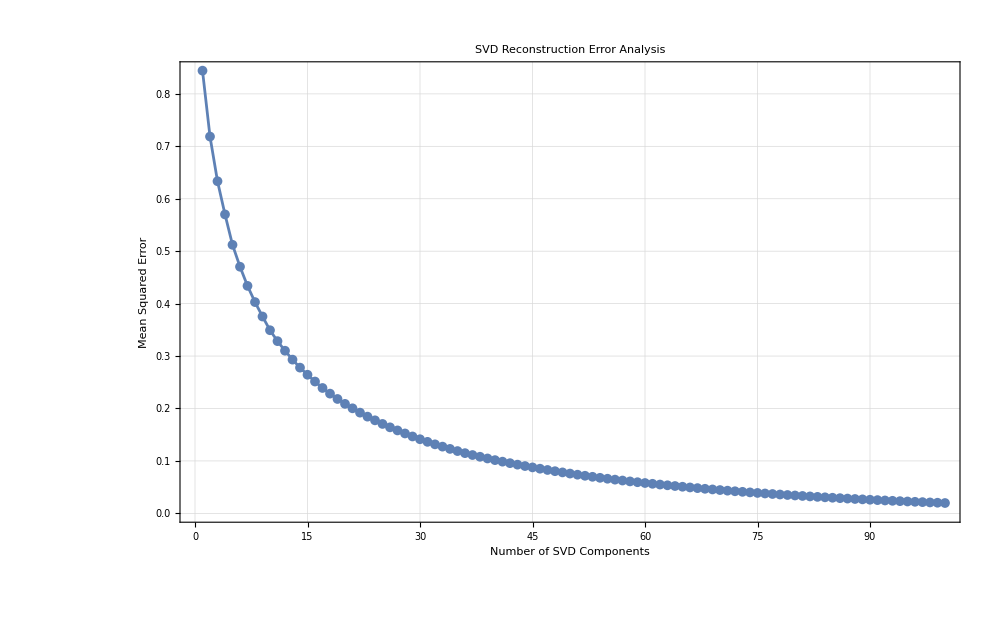

```mathematica
ListLinePlot[componentErrors,PlotRange->All,Frame->True,FrameLabel->{"Number of SVD Components","Mean Squared Error"},PlotLabel->"SVD Reconstruction Error Analysis",PlotStyle->{Thickness[0.002],ColorData[97,1]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotMarkers->{Automatic,Medium},ImageSize->1000]
```

```mathematica
explainedVariance=Accumulate[s^2]/Total[s^2];

(*Find the number of components explaining 95% of the variance*)
numComponentsFor95Percent=First[FirstPosition[explainedVariance,_?(#>=0.95&)]];

Print["Number of components explaining 95% of variance: ",numComponentsFor95Percent];
```

Number of components explaining 95% of variance: 66

```mathematica
componentErrors[[Range[numComponentsFor95Percent]]]
```

{{1,0.844312},{2,0.7186},{3,0.633455},{4,0.570125},{5,0.512164},{6,0.470361},{7,0.43384},{8,0.402923},{9,0.375449},{10,0.34925},{11,0.328449},{12,0.310167},{13,0.293207},{14,0.277911},{15,0.264374},{16,0.251417},{17,0.239114},{18,0.228344},{19,0.218141},{20,0.208813},{21,0.200335},{22,0.192089},{23,0.184466},{24,0.177429},{25,0.17055},{26,0.16406},{27,0.158185},{28,0.152393},{29,0.146645},{30,0.141364},{31,0.136387},{32,0.131642},{33,0.12726},{34,0.122935},{35,0.118803},{36,0.114846},{37,0.111237},{38,0.107946},{39,0.104687},{40,0.101524},{41,0.0985932},{42,0.0957333},{43,0.0928885},{44,0.0902396},{45,0.0876702},{46,0.0851634},{47,0.082755},{48,0.0804146},{49,0.0781106},{50,0.0758844},{51,0.0737316},{52,0.0716758},{53,0.0697177},{54,0.0677882},{55,0.06603},{56,0.0643111},{57,0.0626126},{58,0.0609443},{59,0.0593925},{60,0.0578728},{61,0.0563862},{62,0.054938},{63,0.0535286},{64,0.0521386},{65,0.0507586},{66,0.0494166}}